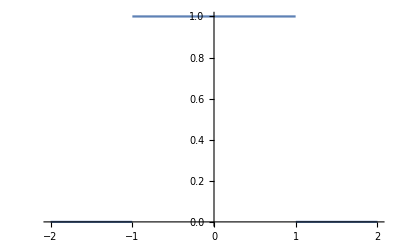

```mathematica
boxfunc[x_, w_]:=UnitStep[x+w]-UnitStep[x-w];
Plot[boxfunc[x,1],{x,-2,2}]
```

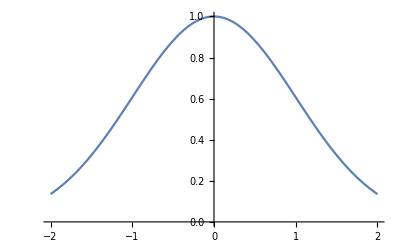

```mathematica
gaussfunc[x_,σ_]:=1/(√(2 σ^2))Exp[-x^2/(2 σ^2)];
Plot[gaussfunc[x,1],{x,-2,2}]
```

```mathematica
combo=Convolve[boxfunc[x,w],gaussfunc[x,σ],x,y]
```

-√(π/2) (1/(√(1/σ^2))-σ Erf[(w-y)/(√2 σ)])+√(π/2) (1/(√(1/σ^2))+σ Erf[(w+y)/(√2 σ)])

```mathematica
Simplify[combo]
```

√(π/2) σ (Erf[(w-y)/(√2 σ)]+Erf[(w+y)/(√2 σ)])

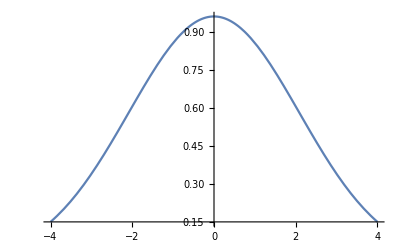

```mathematica
Plot[combo/(2w)/.{w->1,σ->2},{y,-4,4}]
```

```mathematica
gaussfunc[x_,σ_,x0_]:=1/(√(2 π σ^2))Exp[(-(x-x0)^2)/(2 σ^2)];
poissonfunc[x_,λ_]:=(λ^x Exp[-λ])/Gamma[x+1];
```

```mathematica
Integrate[poissonfunc[y,λ]gaussfunc[x-y,σ,x0],{y,0,Infinity},Assumptions->{x>0,σ>0,x0>0,λ>0}]
```

Integrate[(ⅇ^(-λ-(x-x0-y)^2/(2 σ^2)) λ^y)/(√(2 π) √(σ^2) Gamma[1+y]),{y,0,∞},Assumptions→{x>0,σ>0,x0>0,λ>0}]

```mathematica
Sum[poissonfunc[y,λ]gaussfunc[x-y,σ,x0],{y,0,Infinity},Assumptions->{x>0,σ>0,x0>0,λ>0}]
```

Sum[(ⅇ^(-λ-(x-x0-y)^2/(2 σ^2)) λ^y)/(√(2 π) √(σ^2) Gamma[1+y]),{y,0,∞},Assumptions→{x>0,σ>0,x0>0,λ>0}]

```mathematica
Integrate[gaussfunc[y,√λ,λ]gaussfunc[x-y,σ,0],{y,-Infinity,Infinity},Assumptions->{x>0,σ>0,x0>0,λ>0}]
```

(ⅇ^(-(x-λ)^2/(2 (λ+σ^2))))/(√(2 π) √(λ+σ^2))

```mathematica
weight[λ_,thresh_]
```